SimulationTools > DataRegion

# DataRegion

A DataRegion is an n-dimensional block of numbers on a uniform regular Cartesian coordinate grid. A DataRegion object contains the block of numbers, as well as the specification of the coordinate grid.
A DataRegion object is printed in Mathematica as DataRegion[name, dims, range] to avoid printing large quantities of data.  To see the full structure, including all the data, use FullForm.  Mathematical, plotting and interpolation functions are defined for DataRegions.

## Working with DataRegions

### Creating DataRegions

ToDataRegion | ReadGridFunction

Functions for creating DataRegions.

Using ToDataRegion[data, origin, spacing] we can create a DataRegion object from the (multidimensional) list data. This data is assumed to be in row-major order, eg. data[[ix,iy,iz]] for the case of 3D data. The DataRegion will have an origin and spacing given by the lists origin = {ox, oy, ...} and spacing = {dx, dy, ...}.  SimulationTools uses row-major order because that is the convention adopted by Mathematica.  Note that this corresponds to “C” order, not “Fortran” order, as used by the Cactus framework.

```mathematica
data=Table[x^2+y,{x,0,1,0.2},{y,0,6,0.6}]
```

{{0.,0.6,1.2,1.8,2.4,3.,3.6,4.2,4.8,5.4,6.},{0.04,0.64,1.24,1.84,2.44,3.04,3.64,4.24,4.84,5.44,6.04},{0.16,0.76,1.36,1.96,2.56,3.16,3.76,4.36,4.96,5.56,6.16},{0.36,0.96,1.56,2.16,2.76,3.36,3.96,4.56,5.16,5.76,6.36},{0.64,1.24,1.84,2.44,3.04,3.64,4.24,4.84,5.44,6.04,6.64},{1.,1.6,2.2,2.8,3.4,4.,4.6,5.2,5.8,6.4,7.}}

```mathematica
d=ToDataRegion[data,{0,0},{0.2,0.6},VariableName->"MyData"]
```

DataRegion[MyData,<6,11>,{{0.,1.},{0.,6.}}]

Multiple DataRegions d1, d2, ... can be merged into a single enclosing one using ToDataRegion[{d1, d2, ...}];

### Getting Information about a DataRegion

ToListOfData | MinCoordinates | CoordinateRanges
ToListOfCoordinates | MaxCoordinates | CoordinateSpacings
ToList | VariableName | ArrayDepth
Dimensions | □ | □

Functions for working with DataRegions.

A 1D DataRegion can be converted to a DataTable object using ToDataTable.

ToListOfData returns the data in the DataRegion as a nested list.

```mathematica
ToListOfData[d]
```

{{0.,0.6,1.2,1.8,2.4,3.,3.6,4.2,4.8,5.4,6.},{0.04,0.64,1.24,1.84,2.44,3.04,3.64,4.24,4.84,5.44,6.04},{0.16,0.76,1.36,1.96,2.56,3.16,3.76,4.36,4.96,5.56,6.16},{0.36,0.96,1.56,2.16,2.76,3.36,3.96,4.56,5.16,5.76,6.36},{0.64,1.24,1.84,2.44,3.04,3.64,4.24,4.84,5.44,6.04,6.64},{1.,1.6,2.2,2.8,3.4,4.,4.6,5.2,5.8,6.4,7.}}

ToListOfCoordinates returns the coordinates of all the points in the DataRegion

```mathematica
ToListOfCoordinates[d]
```

{{{0.,0.},{0.,0.6},{0.,1.2},{0.,1.8},{0.,2.4},{0.,3.},{0.,3.6},{0.,4.2},{0.,4.8},{0.,5.4},{0.,6.}},{{0.2,0.},{0.2,0.6},{0.2,1.2},{0.2,1.8},{0.2,2.4},{0.2,3.},{0.2,3.6},{0.2,4.2},{0.2,4.8},{0.2,5.4},{0.2,6.}},{{0.4,0.},{0.4,0.6},{0.4,1.2},{0.4,1.8},{0.4,2.4},{0.4,3.},{0.4,3.6},{0.4,4.2},{0.4,4.8},{0.4,5.4},{0.4,6.}},{{0.6,0.},{0.6,0.6},{0.6,1.2},{0.6,1.8},{0.6,2.4},{0.6,3.},{0.6,3.6},{0.6,4.2},{0.6,4.8},{0.6,5.4},{0.6,6.}},{{0.8,0.},{0.8,0.6},{0.8,1.2},{0.8,1.8},{0.8,2.4},{0.8,3.},{0.8,3.6},{0.8,4.2},{0.8,4.8},{0.8,5.4},{0.8,6.}},{{1.,0.},{1.,0.6},{1.,1.2},{1.,1.8},{1.,2.4},{1.,3.},{1.,3.6},{1.,4.2},{1.,4.8},{1.,5.4},{1.,6.}}}

ToList returns a list containing all the data and all the coordinates from the DataRegion.

```mathematica
ToList[d]
```

{{{0.,0.,0.},{0.,0.6,0.6},{0.,1.2,1.2},{0.,1.8,1.8},{0.,2.4,2.4},{0.,3.,3.},{0.,3.6,3.6},{0.,4.2,4.2},{0.,4.8,4.8},{0.,5.4,5.4},{0.,6.,6.}},{{0.2,0.,0.04},{0.2,0.6,0.64},{0.2,1.2,1.24},{0.2,1.8,1.84},{0.2,2.4,2.44},{0.2,3.,3.04},{0.2,3.6,3.64},{0.2,4.2,4.24},{0.2,4.8,4.84},{0.2,5.4,5.44},{0.2,6.,6.04}},{{0.4,0.,0.16},{0.4,0.6,0.76},{0.4,1.2,1.36},{0.4,1.8,1.96},{0.4,2.4,2.56},{0.4,3.,3.16},{0.4,3.6,3.76},{0.4,4.2,4.36},{0.4,4.8,4.96},{0.4,5.4,5.56},{0.4,6.,6.16}},{{0.6,0.,0.36},{0.6,0.6,0.96},{0.6,1.2,1.56},{0.6,1.8,2.16},{0.6,2.4,2.76},{0.6,3.,3.36},{0.6,3.6,3.96},{0.6,4.2,4.56},{0.6,4.8,5.16},{0.6,5.4,5.76},{0.6,6.,6.36}},{{0.8,0.,0.64},{0.8,0.6,1.24},{0.8,1.2,1.84},{0.8,1.8,2.44},{0.8,2.4,3.04},{0.8,3.,3.64},{0.8,3.6,4.24},{0.8,4.2,4.84},{0.8,4.8,5.44},{0.8,5.4,6.04},{0.8,6.,6.64}},{{1.,0.,1.},{1.,0.6,1.6},{1.,1.2,2.2},{1.,1.8,2.8},{1.,2.4,3.4},{1.,3.,4.},{1.,3.6,4.6},{1.,4.2,5.2},{1.,4.8,5.8},{1.,5.4,6.4},{1.,6.,7.}}}

Dimensions returns a list {nx, ny, nz, ...} containing the number of points in each direction.

```mathematica
Dimensions[d]
```

{6,11}

MinCoordinates returns the minimum coordinates of the DataRegion.

```mathematica
MinCoordinates[d]
```

{0.,0.}

MaxCoordinates returns the maximum coordinates of the DataRegion

```mathematica
MaxCoordinates[d]
```

{1.,6.}

VariableName returns a string containing the name of the DataRegion.  This name can be set using the Variable option of ToDataRegion.

```mathematica
VariableName[d]
```

MyData

CoordinateRanges returns a list of the form {{xmin, xmax}, {ymin, ymax}, {zmin, zmax}, ...} describing the minimum and maximum coordinates of the DataRegion.

```mathematica
CoordinateRanges[d]
```

{{0.,1.},{0.,6.}}

CoordinateSpacings returns the spacing between points in the DataRegion in each direction.

```mathematica
CoordinateSpacings[d]
```

{0.2,0.6}

ArrayDepth returns an integer corresponding to the dimensionality of the data.

```mathematica
ArrayDepth[d]
```

2

### Manipulating DataRegions

The Interpolation function has been overloaded to work on DataRegion objects. The resulting function will generically be a function of n variables, where n is the dimensionality of the data.

```mathematica
f=Interpolation[d]
```

InterpolatingFunction[{{0.,1.},{0.,6.}},<>]

```mathematica
f[0.12222,5.78]
```

5.79494

Perform a line integral using the interpolating function:

```mathematica
NIntegrate[f[t,t^2],{t,0,1}]
```

0.666667

The Part function, i.e. d[[2]] etc, has been overloaded to work on DataRegion objects. You can extract a single value, for example d[[3,8,1]], or a lower-dimensional DataRegion, d[[All,All,12]].  You can also specify ranges of indices: d[[All,3;;8,12]].  Unless the result is a single point, the returned value is always a DataRegion.

The Slab function allows you to extract part of a DataRegion by coordinate rather than by index, as in Part above.  For example, if you have a 3D DataRegion and you want to obtain a slice in the xy plane at z = 3.5,  you can use d[[All,All,3.5]].  You can also specify coordinate ranges:  d[[-2.0;;+2.0, -2.0;;+2.0, 3.5]].

```mathematica
d
```

DataRegion[MyData,<6,11>,{{0.,1.},{0.,6.}}]

```mathematica
d2=Slab[d,All,3.0]
```

DataRegion[MyData,<6>,{{0.,1.}}]

### Plotting functions

ListPlot | ArrayPlot
ListLinePlot | ListPlot3D
ListDensityPlot | ListContourPlot

Plotting functions.

Several standard Mathematica plotting functions have been modified to work also with DataRegions.

ListPlot and ListLinePlot can be used with 1-dimensional DataRegions.

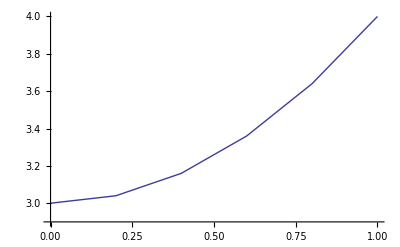

```mathematica
ListLinePlot[d2]
```

ListDensityPlot, ArrayPlot, ListPlot3D and ListContourPlot can be used with 2-dimensional DataRegions.  The DataRange option is computed automatically from the coordinate information in the DataRegion.

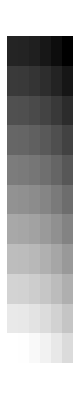

```mathematica
ArrayPlot[d,FrameTicks->True]
```

```mathematica
ListPlot3D[d]
```

-Graphics3D-

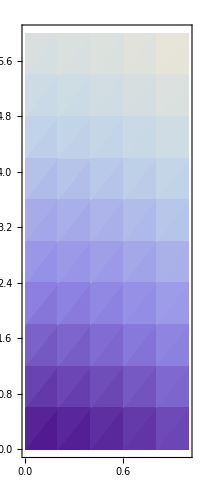

```mathematica
ListDensityPlot[d,AspectRatio->Automatic]
```

Outline produces a Graphics object (Line, Rectangle or Cuboid) with a shape corresponding to that of the DataRegion.

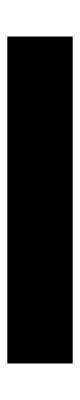

```mathematica
Graphics[Outline[d]]
```

### Mathematical functions

```mathematica
d3=ToDataRegion[Table[x^3-y,{x,0,1,0.2},{y,0,6,0.6}],{0,0},{0.2,0.6}]
```

DataRegion[<<unnamed>>,<6,11>,{{0.,1.},{0.,6.}}]

You can perform many mathematical operations directly on DataRegions:

```mathematica
d+d3
```

DataRegion[MyData,<6,11>,{{0.,1.},{0.,6.}}]

```mathematica
d-d3
```

DataRegion[MyData,<6,11>,{{0.,1.},{0.,6.}}]

```mathematica
3.0*d
```

DataRegion[MyData,<6,11>,{{0.,1.},{0.,6.}}]

```mathematica
Sin[d]
```

DataRegion[MyData,<6,11>,{{0.,1.},{0.,6.}}]

```mathematica
Log10[d]
```

DataRegion[MyData,<6,11>,{{0.,1.},{0.,6.}}]

RELATED TUTORIALS

CarpetHDF5

DataTable

NumericalRelativity